-Graphics3D-

-Graphics3D-

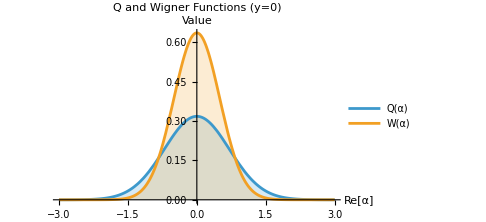

```mathematica
(*Definition of quasi-probability functions Q and W for vacuum state*)(*Note:α=x+i y, |α|^2=x^2+y^2*)(*1. Q function (Husimi) for vacuum state*)QFunctionVacuum[x_,y_]:=(1/Pi)*Exp[-(x^2+y^2)]

(*2. Wigner function for vacuum state*)
WignerFunctionVacuum[x_,y_]:=(2/Pi)*Exp[-2*(x^2+y^2)]

(*--------------------------------------------------------*)
(*a) Plot Q function for vacuum state*)

Plot3D[QFunctionVacuum[x,y],{x,-3,3},{y,-3,3},PlotRange->All,ColorFunction->"BlueGreenYellow",Mesh->None,AxesLabel->{"Re[α] (X1)","Im[α] (X2)","Q(α)"},PlotLabel->Style["Q Function for Vacuum State (Q(α) = 1/π Exp[-|α|^2])",Bold,14],BoxRatios->{1,1,0.5},ImageSize->Large]

(*--------------------------------------------------------*)
(*b) Plot Wigner function for vacuum state*)

Plot3D[WignerFunctionVacuum[x,y],{x,-3,3},{y,-3,3},PlotRange->All,ColorFunction->"BlueGreenYellow",Mesh->None,AxesLabel->{"Re[α] (X1)","Im[α] (X2)","W(α)"},PlotLabel->Style["Wigner Function for Vacuum State (W(α) = 2/π Exp[-2|α|^2])",Bold,14],BoxRatios->{1,1,0.5},ImageSize->Large]

(*--------------------------------------------------------*)
(*c) Simultaneous 2D slice display (for comparing Gaussian widths)*)

Plot[{QFunctionVacuum[x,0],WignerFunctionVacuum[x,0]},{x,-3,3},PlotLabel->Style["Q and Wigner Functions (y=0)",Bold,14],PlotLegends->{"Q(α)","W(α)"},AxesLabel->{"Re[α]","Value"},Filling->{1->Axis,2->Axis},ImageSize->Medium]
```